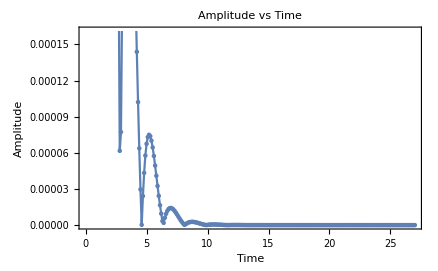

```mathematica
(*Setting variables*)uo=-1*^-4;
ao=0.01;
g=1;
lambdaa=1;
pu=1;
pl=1;
mu=0.03162277660168;
ml=0.03162277660168;

(*Define Capital Lambda s*)
hat[s_]:=Module[{k,Ll,Lu,p1,p2,p3},k=(2*Pi)/lambdaa;
Ll=Sqrt[k^2+s/(ml/pl)];
Lu=Sqrt[k^2+s/(mu/pu)];
p1=-pl*pu*s+k*(mu-ml)*(pu*(k-Ll)-pl*(k-Lu));
p2=k^2*(ml-mu)^2*(k-Ll)*(k-Lu)*(1/s);
p3=(pl+pu)*(pl*(k-Lu)+pu*(k-Ll));
4*k*((p1+p2)/p3)];

(*Define the Laplace-transformed Amplitude*)
Amp[s_]:=Module[{omegaO2,fract},omegaO2=(2*Pi*g)/lambdaa;
fract=(s*uo-omegaO2*ao)/(s^2+hat[s]*s+omegaO2);
(1/s)*(ao+fract)];

(*Specify the time values*)
t3=Range[0.1,27,0.1];

(*Compute the inverse Laplace transform for each time value*)
A3=Abs[InverseLaplaceTransform[Amp[s],s,#]&/@t3];

(*Plot the results*)
ListPlot[Transpose[{t3,Re[A3]}],Frame->True,FrameLabel->{"Time","Amplitude"},PlotLabel->"Amplitude vs Time",Joined->True,Mesh->All]
```